## 无限长圆柱束流包络方程

ρ(t) = (I v)/(π (r(t))^2)

定义微分方程

```mathematica
eqn = y''[x]==1/y[x];
```

设置初始条件

```mathematica
initCond = {y[0]==1,y'[0]==0};
```

数值求解

```mathematica
sol = NDSolve[{eqn,initCond},y,{x,0,100}];
```

绘制解的图像

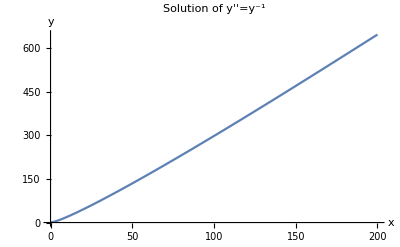

```mathematica
Plot[Evaluate[y[x]/.sol],{x,0,200},PlotRange->All,PlotLabel->"Solution of y''=y^-1",AxesLabel->{"x","y"}]
```

恢复量纲，赋值束流参数

```mathematica
m=9.11 10^-31;e=1.6 10^-19;ϵ0=8.85 10^-12;R=0.01;c=3.0 10^8;
γ[e0_]:=e0/0.511;v[e0_]:=√(1-(1/γ[e0])^2)c;
τ0[e0_,I0_]:=√((2π ϵ0 γ[e0] m v[e0])/(e I0))R;
```

将y[x]参量化为r[L]

```mathematica
rvsL[e0_,I0_]:=100 R Evaluate[y[x]/.sol/.{x->L/(γ[e0] v[e0] τ0[e0,I0])*1000}];
```

绘制图像

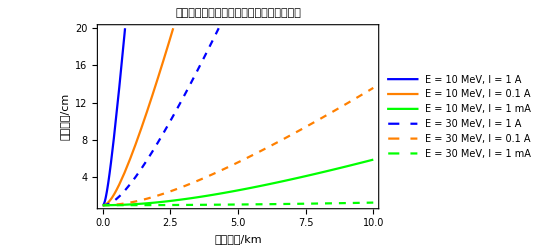

```mathematica
Plot[{rvsL[10,1],rvsL[10,0.1],rvsL[10,10^-3],rvsL[30,1],rvsL[30,0.1],rvsL[30,10^-3]},{L,0,10},PlotRange->{All,{1,20}},PlotLabel->Style["不同束流参数下扩散半径与传输距离的关系",Black,15],PlotStyle->{Blue,Orange,Green,{Blue,Dashed},{Orange,Dashed},{Green,Dashed}},PlotLegends->Placed[LineLegend[{"E = 10 MeV, I = 1 A","E = 10 MeV, I = 0.1 A","E = 10 MeV, I = 1 mA","E = 30 MeV, I = 1 A","E = 30 MeV, I = 0.1 A","E = 30 MeV, I = 1 mA"},LegendMarkerSize->{{20,5}},LabelStyle->Directive[Bold,9]],{0.65,0.75}],Frame->True,FrameLabel->{Style["传输距离/km",Black,12],Style["束流半径/cm",Black,12]}]
```